ⅇ^((-1+ⅈ) ω) √(π/2) (ⅇ^(2 ω) HeavisideTheta[-ω]+HeavisideTheta[ω])

ⅇ^((-1-ⅈ) ω) √(π/2) (ⅇ^(2 ω) HeavisideTheta[-ω]+HeavisideTheta[ω])

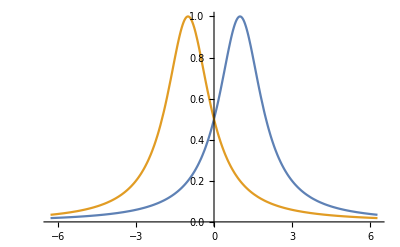

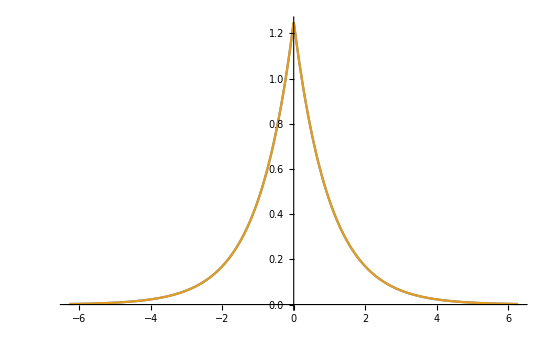

```mathematica
f[t_]= Sin[t] * Sin[2t];
h[t_] = 1/(1 + (t-1)^2);
hh[t_] = 1/(1 + (t+1)^2);
g[t_] = FourierTransform[h[t], t, ω]
gg[t_] = FourierTransform[hh[t], t, ω]

Plot[{h[t], hh[t]}, {t, -2π, 2π}]
Plot[{ Abs[FourierTransform[h[t], t, ω]], Abs[FourierTransform[hh[t], t, ω]]}, {ω, -2π, 2π}]
```